# Example 2.2[2-body Problem]

AER 4074 - ORBITAL Mechanics
By: Mohammad Khalid Gamal Ali | Sec:2, BN:14

## Initial conditions

```mathematica
ClearAll["Global`*"]
m1=10^26 (*kg*);
m2=10^26 (*kg*);
G=6.674*10^-11 ;
μ=G*(m1+m2);
t0=0;
tf=240;
r1={0,0,0};
r2={3000000,0,0};
v1={10000,20000,30000};
v2={0,40000,0};
```

## Functions

```mathematica
sol=NDSolve[{
RX1''[t]==(G*m2*(RX2[t]-RX1[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,RY1''[t]==(G*m2*(RY2[t]-RY1[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,RZ1''[t]==(G*m2*(RZ2[t]-RZ1[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,RX2''[t]==(G*m2*(RX1[t]-RX2[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,RY2''[t]==(G*m2*(RY1[t]-RY2[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,RZ2''[t]==(G*m2*(RZ1[t]-RZ2[t]))/((RX2[t]-RX1[t])^2+(RY2[t]-RY1[t])^2+(RZ2[t]-RZ1[t])^2)^1.5,
RX1'[0]==v1[[1]],RY1'[0]==v1[[2]],RZ1'[0]==v1[[3]],RX2'[0]==v2[[1]],RY2'[0]==v2[[2]],RZ2'[0]==v2[[3]],RX1[0]==r1[[1]],RY1[0]==r1[[2]],RZ1[0]==r1[[3]],RX2[0]==r2[[1]],RY2[0]==r2[[2]],RZ2[0]==r2[[3]]},{RX1,RY1,RZ1,RX2,RY2,RZ2},{t,t0,tf},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Rx1[t_]=RX1[t]/. sol⟦1⟧;
Ry1[t_]=RY1[t]/. sol⟦1⟧;
Rz1[t_]=RZ1[t]/. sol⟦1⟧;
R1[t_]={Rx1[t],Ry1[t],Rz1[t]};
Rx2[t_]=RX2[t]/. sol⟦1⟧;
Ry2[t_]=RY2[t]/. sol⟦1⟧;
Rz2[t_]=RZ2[t]/. sol⟦1⟧;
R2[t_]={Rx2[t],Ry2[t],Rz2[t]};
Rc[t_]=(R2[t]*m2+m1*R1[t])/(m1+m2);
uT1[t_]=Simplify[R1'[t]/Sqrt[R1'[t].R1'[t]],t∈Reals];
vN1[t_]=Simplify[uT1'[t]/Sqrt[uT1'[t].uT1'[t]],t∈Reals];
vB1[t_]=Simplify[Cross[R1'[t],R1''[t]]/Sqrt[Cross[R1'[t],R1''[t]].Cross[R1'[t],R1''[t]]],t∈Reals];
Simplify[Norm/@{uT1[t],vN1[t],vB1[t]},t∈Reals];

uT2[t_]=Simplify[R2'[t]/Sqrt[R2'[t].R2'[t]],t∈Reals];
vN2[t_]=Simplify[uT2'[t]/Sqrt[uT2'[t].uT2'[t]],t∈Reals];
vB2[t_]=Simplify[Cross[R2'[t],R2''[t]]/Sqrt[Cross[R2'[t],R2''[t]].Cross[R2'[t],R2''[t]]],t∈Reals];
Simplify[Norm/@{uT2[t],vN2[t],vB2[t]},t∈Reals];
```

## 2-Body Motion Relative to Inertial Axes

```mathematica
Animate[Show[Graphics3D[{{Red,Arrow[{R1[Tf],R1[Tf]+uT1[Tf]}]},{Blue,Arrow[{R1[Tf],R1[Tf]+vB1[Tf]}]},{Cyan,Arrow[{R1[Tf],R1[Tf]+vN1[Tf]}]}},PlotRange->{{0,7*10^6},{0,2.5*10^7},{0,11*10^6}},Axes->True,

AxesOrigin->{0,0,0},ImageSize->Medium,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False,PlotLabel -> "2-Body Motion Relative to Inertial Axes"],
Graphics3D[{{Red,Arrow[{R2[Tf],R2[Tf]+uT2[Tf]}]},{Blue,Arrow[{R2[Tf],R2[Tf]+vB2[Tf]}]},{Cyan,Arrow[{R2[Tf],R2[Tf]+vN2[Tf]}]}},PlotRange->{{0,7*10^6},{0,2.5*10^7},{0,11*10^6}}],

Legended[Graphics3D[
{
AbsolutePointSize[12.5],Black,Point[R1[Tf]],
AbsolutePointSize[12.5],Red,Point[R2[Tf]],
AbsolutePointSize[5],Darker[Yellow],Point[Rc[Tf]],


Black,Thick,Line[Table[R1[t],{t,0,Tf}]],
Red,Thick,Line[Table[R2[t],{t,0,Tf}]],
Darker[Yellow],Thick,Line[Table[Rc[t],{t,0,Tf}]],
Black,Dashed,Line[{R2[Tf],R1[Tf]}],


Text[Style["M1",Bold,Black],R1[Tf],{-2,1}],
Text[Style["Rc",Bold,Darker[Yellow]],Rc[Tf],{-2,1}],
Text[Style["M2",Bold,Red],R2[Tf],{-2,1}]

},

PlotRange->{{0,5*10^6},{0,2.5*10^7},{0,11*10^6}},
Axes->True,

AxesOrigin->{0,0,0},ImageSize->Medium,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False
],SwatchLegend[{Black,Red,Darker[Yellow]},{"m1","m2","cg"}]]],
{Tf,0,240}
,AnimationRunning->False,AnimationRate->20]
```

## 2-Body Motion Relative to the center of mass

```mathematica
Animate[Show[Graphics3D[{{Red,Arrow[{R1[Tf]-Rc[Tf],R1[Tf]-Rc[Tf]+uT1[Tf]}]},{Blue,Arrow[{R1[Tf]-Rc[Tf],R1[Tf]-Rc[Tf]+vB1[Tf]}]},{Cyan,Arrow[{R1[Tf]-Rc[Tf],R1[Tf]-Rc[Tf]+vN1[Tf]}]}},PlotRange->{{-2*10^6,2*10^6},{-600000,600000},{-600000,600000}},Axes->True,

AxesOrigin->{0,0,0},ImageSize->Medium,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False,PlotLabel -> "2-Body Motion Relative to the center of mass"],
Graphics3D[{{Red,Arrow[{R2[Tf]-Rc[Tf],R2[Tf]-Rc[Tf]+uT2[Tf]}]},{Blue,Arrow[{R2[Tf]-Rc[Tf],R2[Tf]-Rc[Tf]+vB2[Tf]}]},{Cyan,Arrow[{R2[Tf]-Rc[Tf],R2[Tf]-Rc[Tf]+vN2[Tf]}]}},PlotRange->{{0,7*10^6},{0,2.5*10^7},{0,11*10^6}}],

Legended[Graphics3D[
{
AbsolutePointSize[12.5],Black,Point[R1[Tf]-Rc[Tf]],
AbsolutePointSize[12.5],Red,Point[R2[Tf]-Rc[Tf]],
AbsolutePointSize[5],Darker[Yellow],Point[{0,0,0}],


Black,Thick,Line[Table[R1[t]-Rc[t],{t,0,Tf}]],
Red,Thick,Line[Table[R2[t]-Rc[t],{t,0,Tf}]],

Black,Dashed,Line[{R2[Tf]-Rc[Tf],R1[Tf]-Rc[Tf]}],


Text[Style["M1",Bold,Black],R1[Tf]-Rc[Tf],{-2,1}],
Text[Style["Rc",Bold,Darker[Yellow]],{0,0,0},{-2,1}],
Text[Style["M2",Bold,Red],R2[Tf]-Rc[Tf],{-2,1}]

},


Axes->True,

AxesOrigin->{0,0,0},ImageSize->Medium,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False
],SwatchLegend[{Black,Red,Darker[Yellow]},{"m1","m2","cg"}]]],
{Tf,0,240}
,AnimationRunning->False,AnimationRate->20]
```

## 2-Body Motion Relative to m1

```mathematica
Animate[Show[Graphics3D[{{Red,Arrow[{R1[Tf]-R1[Tf],R1[Tf]-R1[Tf]+uT1[Tf]}]},{Blue,Arrow[{R1[Tf]-R1[Tf],R1[Tf]-R1[Tf]+vB1[Tf]}]},{Cyan,Arrow[{R1[Tf]-R1[Tf],R1[Tf]-R1[Tf]+vN1[Tf]}]}},PlotRange->{{-1*10^6,4*10^6},{-1000000,1000000},{-1700000,1700000}},Axes->True,

AxesOrigin->{0,0,0},ImageSize->Medium,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False,ImageSize->Large,PlotLabel -> "2-Body Motion Relative to the center of mass"],
Graphics3D[{{Red,Arrow[{R2[Tf]-R1[Tf],R2[Tf]-R1[Tf]+uT2[Tf]}]},{Blue,Arrow[{R2[Tf]-R1[Tf],R2[Tf]-R1[Tf]+vB2[Tf]}]},{Cyan,Arrow[{R2[Tf]-R1[Tf],R2[Tf]-R1[Tf]+vN2[Tf]}]}}],
Legended[Graphics3D[
{
AbsolutePointSize[12.5],Black,Point[{0,0,0}],
AbsolutePointSize[12.5],Red,Point[R2[Tf]-R1[Tf]],
AbsolutePointSize[5],Darker[Yellow],Point[Rc[Tf]-R1[Tf]],
Darker[Yellow],Thick,Line[Table[Rc[t]-R1[t],{t,0,Tf}]],
Red,Thick,Line[Table[R2[t]-R1[t],{t,0,Tf}]],
Black,Dashed,Line[{R2[Tf]-R1[Tf],Rc[Tf]-R2[Tf]}],
Text[Style["M1",Bold,Black],{0,0,0},{-2,1}],
Text[Style["Rc",Bold,Darker[Yellow]],Rc[Tf]-R1[Tf],{-2,1}],
Text[Style["M2",Bold,Red],R2[Tf]-R1[Tf],{-2,1}]
},Axes->True,AxesOrigin->{0,0,0},ImageSize->Large,AxesLabel->{"X","Y","Z"},Axes->True,AxesStyle->Black,Boxed->False
],SwatchLegend[{Black,Red,Darker[Yellow]},{"m1","m2","cg"}]]],
{Tf,0,240},AnimationRunning->False,AnimationRate->20]
```

## Angular Momentum

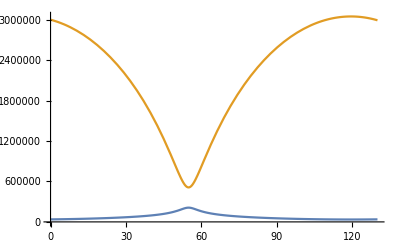

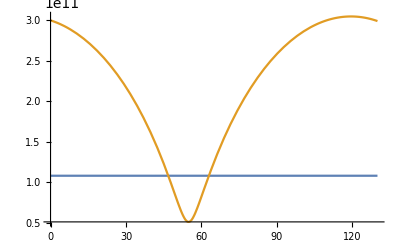

```mathematica
ClearAll[h,CU,CV]
CU[t_]=-R1[t]+R2[t];
CV[t_]=-R1'[t]+R2'[t];
h[t_]=Cross[CU[t],CV[t]];
Plot[{Norm[CV[t]],Norm[CU[t]]},{t,0,130}]
Plot[{Norm[h[t]],10^5*Norm[CU[t]]},{t,0,130}]
```

## Velocity Plots

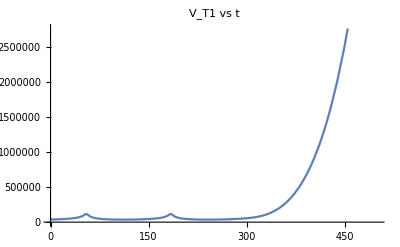

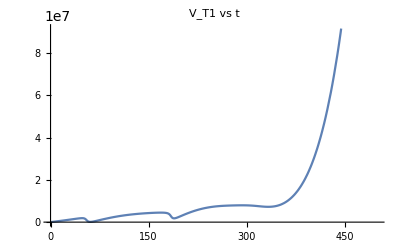

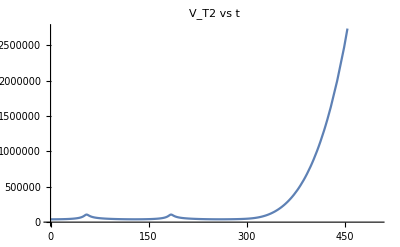

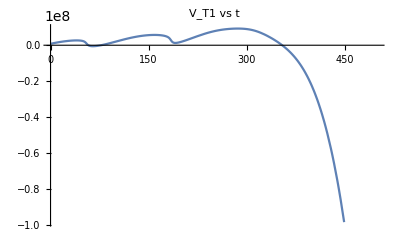

```mathematica
Plot[{R1'[t].uT1[t]},{t,0,500},PlotLabel -> "V_T1 vs t"]
Plot[{R1[t].uT1[t]},{t,0,500},PlotLabel -> "V_T1 vs t"]
Plot[{R2'[t].uT2[t]},{t,0,500},PlotLabel -> "V_T2 vs t"]
Plot[{R2[t].uT1[t]},{t,0,500},PlotLabel -> "V_T1 vs t"]
```

## Conservation of Energy

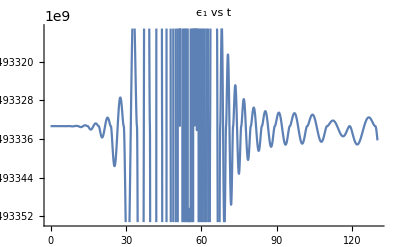

```mathematica
ClearAll[ϵ]
ϵ[t_]=0.5*(CV[t].CV[t])-μ/Sqrt[(CU[t].CU[t])];
Plot[{ϵ[t]},{t,0,130},PlotLabel -> "ϵ_1 vs t"]
```